# ELLIPSES

## Q16.What is an ellipse?

An ellipse is a closed curve similar to a circle.However, the radius
varies between a minimum diameter and a maximum diameter.In effect, an ellipse can be considered to be a squashed or stretched
circle.An axis - aligned ellipse can be specified as a centre (x_0, y_0) and
axis radii (a, b)

These can be combined to give the equation :

```mathematica
(x-x0)^2/a^2+(y-y0)^2/b^2 -1==0
```

-1+(x-x0)^2/a^2+(y-y0)^2/b^2==0

Expnding out this expression will generate an equation identical to that
of a circle.However, the values of A and B are not guaranteed to be
equal to one.The algebraic expression is :

```mathematica
{Axx,Axy,Ayy,Ax,Ay,A0}.{x^2,x y, y^2,x,y,1}==0
```

A0+Ax x+Axx x^2+Ay y+Axy x y+Ayy y^2==0

where {Axx,Axy,Ayy,Ax,Ay,A0} are constant terms.

## Q17.How do I calculate the Y coordinate if only the X coordinate is known?

Given the equation :

[1] Ax + By + Cx + Dy + Exy + F = 0

Then the known value of x or y is defined as : [2]

x = X

y = Y

Substituting[2] into[1] gives : 2 2

[3] AX + By + CX + Dy + EXy + F = 0

2 2
Ax + BY + Cx + DY + ExY + F = 0

Moving all constant terms to the end of the equation gives : 2 2

[4] By + Dy + EXy + AX + CX + F = 0

2 2
Ax + Cx + ExY + BY + DY + F = 0

Converting these into quadratic equations gives : 2 2

Ry + Sy + T = 0 Rx + Sx + T = 0

where : R = B R = A

S = D + Ey S = C + EY

2 2
T = AX + CX + F T = BY + DY + F

These values can be solved using quadratic equations.

## Q18.How do I determine the gradient of a point on a ellipse?

```mathematica
The equation of the ellipse is : 2 2
Ax + By + Cx + Dy + Exy + F = 0

The values of dx and dy are calculated from : dx = 2 Ax + C + Ey

dy = 2 By + D + Ex

The gradient is calculated from : dy 2 By + D + Ex
M = -- = ------------dx 2 Ax + C + Ey
```

## Q19.How do I determine the outward normal of a point on the ellipse?

```mathematica
The equation of the ellipse is : 2 2
Ax + By + Cx + Dy + Exy + F = 0

The values of dx and dy are calculated from : dx = 2 Ax + C + Ey

dy = 2 By + D + Ex

The outward normal is calculated from : N = (dy, -dx)
```

## Q20.How do I calculate the coefficients of an axis - aligned ellipse?

```mathematica
The algebraic exprssion of an ellipse is : 2 2
Ax + By + Cx + Dy + Exy + F = 0

where A, B, C, D, E and F are constant terms.Multiplying out the denominators in[1] gives : 2 2 2 2 2 2
s (x - c) + r (y - d) - r s = 0

Multiplying out the numerators in[1] gives : 2 2 2 2 2 2 2 2
s (x - 2 cx + c) + r (y - 2 dy + d) - r s = 0

Converting into single terms produces : 2 2 2 2 2 2 2 2 2 2 2 2
s x - s 2 cx + s c + r y - r 2 dy + r d - r s = 0

Multiplying every parameter by the denominator gives : 2 2 2 2 2 2 2 2 2 2 2 2
s x - s 2 cx + s c + r y - r 2 dy + r d - r s = 0

Rearranging into the algebraic expression gives : 2 2 2 2 2 2 2 2 2 2 2 2
s x + r y - s 2 cx - r 2 dy + r d + s c - r s = 0

The values of the constant terms are then as follows : 2
A = s

2
B = r

2
C = -s 2 c

2
D = -r 2 d


E = 0

2 2 2 2 2 2
F = r d + s c - r s

For an axis - aligned ellipse, A and B are always positive.For an axis - aligned ellipse, E is always zero, and F is always negative.These constants can be used to render the ellipse using an incremental
scan - line algorithm.
```

## Q21.How do I calculate the coefficients of an arbitary rotated ellipse?

The parameters calculated previously are only correct for an ellipse
which is aligned with the X and Y axii.The ellipse still has to be rotated by the desired angle.This is done
as follows : Rotating a pair of X and Y coordinates can be performed by the following
expression :

```mathematica
Row[{MatrixForm[RotationMatrix[θ]]," . ",MatrixForm[{x,y}]," = ",RotationMatrix[θ].{x,y}}]
```

(Cos[θ] | -Sin[θ]
Sin[θ] | Cos[θ]) . (x
y) = {x Cos[θ]-y Sin[θ],y Cos[θ]+x Sin[θ]}

Substituting the resulting matrix elements into equation[1] gives : 2 2

```mathematica
-1+((y-y0) Cos[θ]+(x-x0)  Sin[θ])^2/b^2+((x-x0) Cos[θ]-(y-y0) Sin[θ])^2/a^2==0
```

```mathematica
(x)^2/a^2+(y)^2/b^2 -1==0/.{x->x Cos[θ]-y Sin[θ],y->y Cos[θ]+x Sin[θ]}
out1=%/.{x->(x-x0),y->(y-y0)}
```

-1+(y Cos[θ]+x Sin[θ])^2/b^2+(x Cos[θ]-y Sin[θ])^2/a^2==0

-1+((y-y0) Cos[θ]+(x-x0) Sin[θ])^2/b^2+((x-x0) Cos[θ]-(y-y0) Sin[θ])^2/a^2==0

Multiplying out the denominators gives : 
Multiplying out the equations within the parenthesis gives :
Then rearranging into the order required by equation[2] gives :

```mathematica
Expand[a^2 b^2 (out1[[1]])];
out2=Collect[%,{x,y}]==0
```

-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2+x^2 (b^2 Cos[θ]^2+a^2 Sin[θ]^2)+y^2 (a^2 Cos[θ]^2+b^2 Sin[θ]^2)+y (-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2)+x (-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2+y (2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ]))==0

```mathematica
{{A0,Ay,Ayy},{Ax,Axy,Axyy},{Axx,Axxy,Axxyy}}=CoefficientList[out2[[1]],{x,y}];
Row[{MatrixForm[{{"A0","Ay","Ayy"},{"Ax","Axy","Axyy"},{"Axx","Axxy","Axxyy"}}]," = ",MatrixForm[{{A0,Ay,Ayy},{Ax,Axy,Axyy},{Axx,Axxy,Axxyy}}]}]
```

(A0 | Ay | Ayy
Ax | Axy | Axyy
Axx | Axxy | Axxyy) = (-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2 | -2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2 | a^2 Cos[θ]^2+b^2 Sin[θ]^2
-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2 | 2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ] | 0
b^2 Cos[θ]^2+a^2 Sin[θ]^2 | 0 | 0)

The values of the constant terms are then as follows :

```mathematica
Row[{MatrixForm[{"Axx","Axy","Ayy","Ax","Ay","A0"}]," = ",MatrixForm[{Axx,Axy,Ayy,Ax,Ay,A0}]}]
```

(Axx
Axy
Ayy
Ax
Ay
A0) = (b^2 Cos[θ]^2+a^2 Sin[θ]^2
2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ]
a^2 Cos[θ]^2+b^2 Sin[θ]^2
-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2
-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2
-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2)

```mathematica
TableForm[Map[(Row[{#[[1]]<>"=",#[[2]],";"}])&,Transpose[{{"Axx","Axy","Ayy","Ax","Ay","A0"},{Axx,Axy,Ayy,Ax,Ay,A0}}]]]
```

Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2;
Axy=2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ];
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2;
Ax=-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2;
Ay=-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2;
A0=-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2;

```mathematica
Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2;
Axy=2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ];
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2;
Ax=-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2;
Ay=-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2;
A0=-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2;
```

These values tend to get quite large, so 64 - bit integers will be
required.

```mathematica
Clear[EllipseCoeffsFromProperties]
EllipseCoeffsFromProperties[{{x0_,y0_},{a_,b_},θ_}]:=Module[{Axx,Axy,Ayy,Ax,Ay,A0},
Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2;
Axy=2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ];
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2;
Ax=-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2;
Ay=-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2;
A0=-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2;
{Axx,Axy,Ayy,Ax,Ay,A0}
]
```

```mathematica
Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2
Axy=-2 a^2 Cos[θ] Sin[θ]+2 b^2 Cos[θ] Sin[θ]
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2
Ax=-2 b^2 x0 Cos[θ]+2 a^2 y0 Sin[θ]
Ay=-2 a^2 y0 Cos[θ]-2 b^2 x0 Sin[θ]
A0=-a^2 b^2+b^2 x0^2+a^2 y0^2
```

-1225.+48.0527 x^2-9.34604 x y+25.9473 y^2==0

{7.91597×10^-25 (2.27511×10^23 x-2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2)),7.91597×10^-25 (2.27511×10^23 x+2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2))}

900-539.833 x+48.0527 x^2-196.672 y-9.34604 x y+25.9473 y^2==0

{9.39639×10^-37 (4.03329×10^36+1.91666×10^35 x-8.09121×10^8 √(-3.51589×10^55+3.83547×10^55 x-3.14777×10^54 x^2)),9.39639×10^-37 (4.03329×10^36+1.91666×10^35 x+8.09121×10^8 √(-3.51589×10^55+3.83547×10^55 x-3.14777×10^54 x^2))}

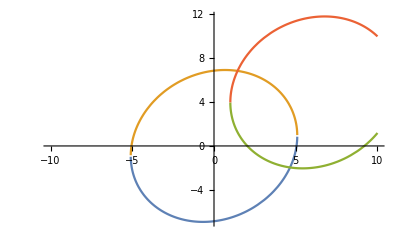

```mathematica
EllipseCoeffsFromProperties[{{0,0},{5,7},0.2}].{x^2,x y, y^2,x,y,1}==0
f1=y/.Solve[%,{x,y}]
EllipseCoeffsFromProperties[{{5,6},{5,7},0.2}].{x^2,x y, y^2,x,y,1}==0
f2=y/.Solve[%,{x,y}]
Plot[{f1,f2},{x,-10,10}]
```

```mathematica
Solve[%,{x,y}]
```

{{y→7.91597×10^-25 (-2.27511×10^23 x-2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2))},{y→7.91597×10^-25 (-2.27511×10^23 x+2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2))}}